# Walker — Problem Set 13

## Section 33

```mathematica
Head[ListPlot[{0,2}]]
```

Graphics

```mathematica
Times@@Range[100]
```

93326215443944152681699238856266700490715968264381621468592963895217599993229915608941463976156518286253697920827223758251185210916864000000000000000000000000

```mathematica
f@@@Tuples[{a,b},2]
```

{f[a,a],f[a,b],f[b,a],f[b,b]}

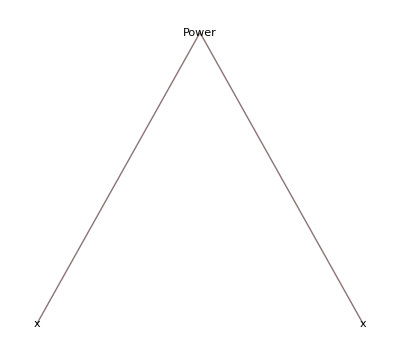
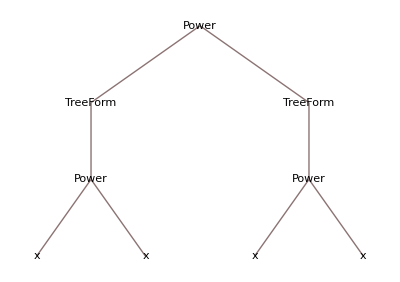
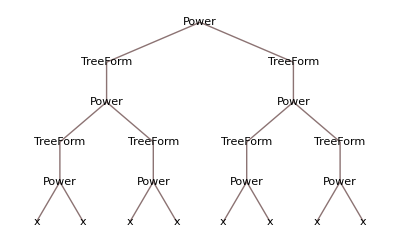
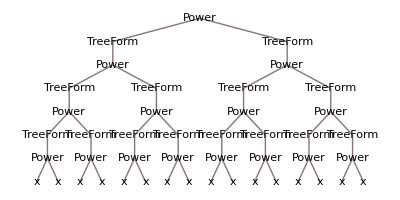
{x,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
NestList[TreeForm[#^#]&,x,4]
```

```mathematica
Union[Cases[Flatten[Table[i^2/(j^2+1),{i,20},{j,20}]],_Integer]]
```

{2,5,8,10,17,18,20,32,40,45,50,72,80,98,128,162,200}

```mathematica
Graph[Rule@@@Partition[Table[Mod[n^2+n,100],{n,100}],2,1]]
```

-Graphics-

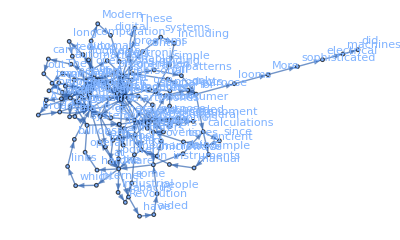

```mathematica
Graph[Rule@@@Partition[Take[TextWords[WikipediaData["computers"]],200],2,1],VertexLabels->All]
```

```mathematica
f@@@{{1,2},{7,2},{5,4}}
```

{f[1,2],f[7,2],f[5,4]}

## Section 34

```mathematica
Counts[Sort[IntegerDigits[3^100]]]
```

<|0→7,1→9,2→9,3→5,4→1,5→5,6→4,7→7,9→1|>

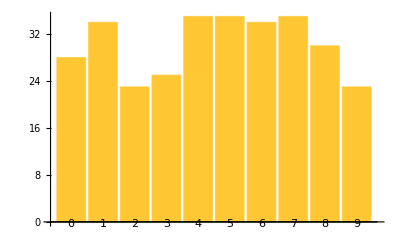

```mathematica
BarChart[Counts[Sort[IntegerDigits[2^1000]]],ChartLabels->Automatic]
```

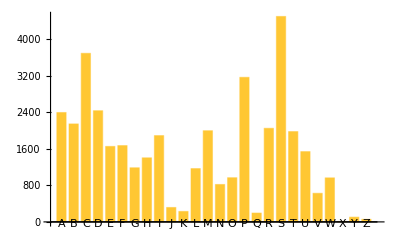

```mathematica
BarChart[Counts[First/@Characters/@ToUpperCase/@WordList[]],ChartLabels->Automatic]
```

```mathematica
Take[Reverse[Sort[Counts[First/@Characters/@WordList[]]]],5]
```

<|s→4499,c→3693,p→3168,d→2433,a→2393|>

```mathematica
Take[Reverse[Sort[Counts[First/@Characters/@WordList[]]]],5]
```

<|s→4499,c→3693,p→3168,d→2433,a→2393|>

```mathematica
N[#q/#u]&[LetterCounts[WikipediaData["computers"]]]
```

0.0401274

```mathematica
Keys[Take[Reverse[Sort[Counts[TextWords[ExampleData[{"Text","AliceInWonderland"}]]]]],10]]
```

{the,and,a,to,she,of,was,Alice,in,it}